```mathematica
S=Solve[r*x+4 x^3-9 x^5==0,x]//Flatten
```

{x→0,x→-1/3 √(2-√(4+9 r)),x→1/3 √(2-√(4+9 r)),x→-1/3 √(2+√(4+9 r)),x→1/3 √(2+√(4+9 r))}

```mathematica
(* Lines *)
p1=Plot[S⟦1⟧[[2]],{r,-1,0},PlotStyle->Blue,AxesLabel->{r,x}];p2=Plot[S⟦1⟧[[2]],{r,0,1},PlotStyle->{Blue, Dashed},AxesLabel->{r,x}];
p3=Plot[S⟦2⟧[[2]],{r,-1,0},PlotStyle->{Blue, Dashed},AxesLabel->{r,x}];
p4=Plot[S⟦3⟧[[2]],{r,-1,0},PlotStyle->{Blue, Dashed},AxesLabel->{r,x}];
p5=Plot[S⟦4⟧[[2]],{r,-1,1},PlotStyle->Blue,AxesLabel->{r,x}];
p6=Plot[S⟦5⟧[[2]],{r,-1,1},PlotStyle->Blue,AxesLabel->{r,x}];
```

Syntax::sntxf: "{r,x^*" cannot be followed by "}".

```mathematica
rc = -4/9;
bp1 ={rc, S[[2]][[2]]/.r->rc};
bp2 ={rc, S[[3]][[2]]/.r->rc};
pb= ListPlot[{bp1,bp2}, PlotMarkers->{Automatic, 10}, PlotStyle->Blue, PlotLegends->{"Saddle-node bifurcation"}];
ps= ListPlot[{{0,0}}, PlotMarkers->{Automatic, 10}, PlotStyle->Red, PlotLegends->{"Subcritical pitchfork bifuraction"}];
```

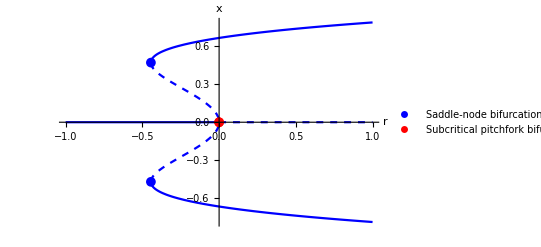

```mathematica
Show[p1,p2,p3,p4,p5,p6,pb,ps,PlotRange->Full]
```